# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data/Scalars"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data/Scalars"}]]];
tagslist={"Evaluation","Evaluation-sensitivity"};
choiceslist={"Tabulated number of events+sensitivity","Sensitivity only"};
computationchoice=dropdownDialog[choiceslist,"Do you want to compute the tabulated number of events and then sensitivity, or just sensitivity (if the tabulate number of events has been already produced)?"];
tagselected=If[computationchoice=="Tabulated number of events+sensitivity","Evaluation","Evaluation-sensitivity"];
BlockEvaluation[tagselected]
```

# Preliminary definitions

## Parameters and various functions

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
(*chbar*)
chbar= 6.6*10^-25*3*10^8;
(*Masses of various SM particles*)
mB=5.3;
mK=0.495;
mπ=0.14;
mh=125;
mBs=5.366;
(*Fragmentation fractions at the LHC*)
fbtob0LHC=fbtobplusLHC=0.324;
fbtobsLHC=0.09;
fstoK0L=1/4;
fstoKcharged=1/2;
(*Fragmentation fractions at SPS*)
fbtobsSPS=0.11;
fbtob0SPS=fbtobplusSPS=0.411;
fstokplusSPS=0.5;
(*Fraction of K^(+/-) decaying in-flight, from https://arxiv.org/pdf/2004.07974.pdf*)
fractionDecayInFlightKplusKminus=(0.29+0.07);
(*Fragmentation fractions at FermilabBD. Assumed to be the same as at SPS*)
fbtobsFermilabBD=0.11;
fbtob0FermilabBD=fbtobplusFermilabBD=0.411;
```

## Scalar phenomenology

## Proton bremsstrahlung probability

### Various parameters

```mathematica
MP=0.938;
(*Scalar-nucleon low-energy coupling*)
GSNN=1.2*10^-3;
(*Fit for the pp total cross-section in mb in terms of invariant mass s*)
Zfit=35.45;
Bfit=0.308;
Y1fit=42.53;
Y2fit=33.34;
s0fit=5.38^2;
s1fit=1;
η1fit=0.458;
η2fit=0.545;
S[Pp_,mp_]=2*Pp*mp;
Sprime[Pp_,mp_,z_]=2*mp*Pp(1-z)+2*mp^2;
sigmapp[s_]=Zfit+Bfit*Log[s/s0fit]^2+Y1fit*(s1fit/s)^η1fit-Y2fit(s1fit/s)^η2fit;
(*Kinematics of the 1 -> 2 process p -> p + S within the WW approximation*)
EPbrem=Pp+mp^2/(2*Pp);
EpprimeBrem=Pp*(1-z)+(mp^2+pT^2)/(2*Pp(1-z));
ppprimeBrem=(1-z)*Pp;
ESbrem=Pp*z+(pT^2+mS^2)/(2*Pp*z);
pSbrem=pp-ppprimeBrem;
Print["Applicability parameter (must be << 1):"]
ApplicabilityParameter[Pp_,z_,pT_,mX_,mp_]=Simplify[(EpprimeBrem+ESbrem-EPbrem)/((EpprimeBrem-ESbrem+EPbrem)/.{pT->0,mp->0,mX->0})]/.{mS->mX}/.{mX^2+4 Pp^2 (z-1) z->4 Pp^2 z(z-1)}
(*Momenta of the protons at various facilities*)
{Ppfacility["SPS"],Ppfacility["LHC"],Ppfacility["FCC-hh"],Ppfacility["FermilabBD"]}={400.,7000.,50000.,120.};
(*The minimal allowed fraction of energy Subscript[E, S]/Subscript[E, p]*)
{zMinBrem["FermilabBD"],zMinBrem["SPS"],zMinBrem["LHC"],zMinBrem["FCC-hh"]}={0.1,0.1,0.005,0.0001};
(*The maximal allowed fraction of energy*)
zMaxBrem=0.9;
(*Elastic SNN form-factor*)
BremFormFactorSquared[mS_]=Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/branching ratios/proton-timelike-form-factor-scalar.txt"}],"Table"],InterpolationOrder->1][mS];
```

Applicability parameter (must be << 1):

(pT^2-mX^2 (-1+z)+mp^2 z^2)/(4 Pp^2 (-1+z)^2 z)

### Distribution

```mathematica
<<FeynCalc`
(*Matrix element corresponding to the sub-process p -> p + S*)
MscalarBrem=gSNN SpinorUBar[p1,mp].SpinorU[k1,mp];
MscalarBremStar=ComplexConjugate[MscalarBrem];
(*Squared matrix element*)
MScalarBremSquared=(1/2 FermionSpinSum[MscalarBrem MscalarBremStar]/.DiracTrace->TR//Contract//Simplify)/.{ScalarProduct[k1,p1]-> Pp*EpprimeBrem-Pp*ppprimeBrem};
(*Differential splitting probability*)
DifferentialSplittingProbability[mp_,mS_,pT_,z_,gSNN_,Pp_]=Simplify[(1/(16*Pi^2*z)1/(4*Pp*EpprimeBrem)*MScalarBremSquared/(EpprimeBrem+ESbrem-Pp)^2)]/.{ (mp^2+2 Pp^2) ->2*Pp^2}/.{mp^2+2 Pp^2 (z-1)^2+pT^2->2*Pp^2(z-1)^2};
pTmaxBrem=DialogInput[{br=""},Column[{"Enter the maximal p_T (in GeV) for the bremsstrahlung channel (typical value is 1 GeV):",InputField[Dynamic[br],Number],Button["Proceed",DialogReturn[br],ImageSize->Automatic]}]]//N;
(*Double distribution in θ and E*)
DistrBremInpTz[mS_,pT_,z_,Pp_,zmin_]=DifferentialSplittingProbability[MP,mS,pT,z,GSNN,Pp]*2*pT*sigmapp[Sprime[Pp,MP,z]]/sigmapp[S[Pp,MP]] UnitStep[pTmaxBrem-pT]*UnitStep[z-zmin]UnitStep[zMaxBrem-z];
pTinθE[θS_,ES_,mS_]=√(ES^2-mS^2)Sin[θS];
zInθE[ES_,Pp_]=ES/Pp;
JacobianpTzToESθS[θS_,ES_]=D[pTinθE[θS,ES,mS],θS]*D[zInθE[ES,Pp],ES];
DistrBremθEscalarNoFormFactorTemp[mS_,θS_,ES_,Pp_,zmin_]=DistrBremInpTz[mS,pTinθE[θS,ES,mS],zInθE[ES,Pp],Pp,zmin]*JacobianpTzToESθS[θS,ES];
{mSminFromBrem,mSmaxFromBrem}={0.02,2.5};
ESmaxBremBeam[Facility_,θS_]:=Min[zMaxBrem*Ppfacility[Facility],pTmaxBrem/(Sin[θS]+10^-7)];
θmaxBremTemp[Facility_]:=(θS/.Solve[zMinBrem[Facility]*Ppfacility[Facility]==pTmaxBrem/Sin[θS],θS][[1]]/.{C[1]->0});
{θmaxBremFacility["FermilabBD"],θmaxBremFacility["SPS"],θmaxBremFacility["LHC"],θmaxBremFacility["FCC-hh"]}=θmaxBremTemp[#]&/@{"FermilabBD","SPS","LHC","FCC-hh"};
NormalizationBremNoFormFactorTemp[Facility_]:=Module[{zmin,ESmaxfrombrem,pbeam,θmaxbrem},
pbeam=Ppfacility[Facility];
zmin=zMinBrem[Facility];
ESmaxfrombrem[θS_]=ESmaxBremBeam[Facility,θS];
θmaxbrem=θmaxBremFacility[Facility];
Interpolation[Table[{mS,NIntegrate[DistrBremθEscalarNoFormFactorTemp[mS,θS,ES,pbeam,zmin],{θS,0,θmaxbrem},{ES,zmin*pbeam,Max[zmin*pbeam,ESmaxfrombrem[θS]]},Method->"AdaptiveMonteCarlo"]},{mS,mSminFromBrem,mSmaxFromBrem,(mSmaxFromBrem-mSminFromBrem)/20}],InterpolationOrder->1][mS]
]
Do[NormalizationBremNoFormFactor[mS_,Facility]=NormalizationBremNoFormFactorTemp[Facility];
DoubleDistrScalarfromBremFacility[mS_,θS_,ES_,Facility]=If[mSminFromBrem≤mS≤mSmaxFromBrem,Evaluate[1/NormalizationBremNoFormFactor[mS,Facility]*DistrBremθEscalarNoFormFactorTemp[mS,θS,ES,Ppfacility[Facility],zMinBrem[Facility]]],0];
PbremFacility[mS_,θ2_,Facility]=θ2*BremFormFactorSquared[mS]*NormalizationBremNoFormFactor[mS,Facility];
ESmaxFromBrem[mS_,θS_,Facility]=ESmaxBremBeam[Facility,θS],{Facility,{"FermilabBD","SPS","LHC","FCC-hh"}}];
(*Tabulated distribution to be used in next sections*)
TableBremDistr[θminExp_,θmaxExp_,Facility_]:=Module[{eminbrem,θSlistbrem,EslistBremTemp,EslistBrem},
eminbrem=Ppfacility[Facility]*zMinBrem[Facility];
θSlistbrem=Table[θV,{θV,0.99θminExp,1.01θmaxExp,(1.01θmaxExp-0.99θminExp)/50}];
EslistBremTemp=Join[Table[x,{x,0.02,eminbrem,1}],Table[10^x,{x,Log10[1.02*eminbrem],Log10[Ppfacility[Facility]],(Log10[Ppfacility[Facility]]-Log10[1.02*eminbrem])/50}]];
EslistBrem=Join[EslistBremTemp,ESmaxBremBeam[Facility,#]&/@θSlistbrem]//Sort//DeleteDuplicates;
Flatten[Table[{mS,θS,ES,DoubleDistrScalarfromBremFacility[mS,θS,ES,Facility]+10^-90},{mS,mSminFromBrem,mSmaxFromBrem//N,((mSmaxFromBrem//N)-mSminFromBrem)/10},{θS,θSlistbrem},{ES,EslistBrem}],{1,2,3}]
]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

## Production probabilities from decays

### From decays

#### Br ratios

```mathematica
SetDirectory[NotebookDirectory[]];
(*Branching ratios of the scalar production from B and K mesons through the mixing θ at θ = 1*)
BrBplusToXsS[mS_]=If[mS<mB-mπ,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/branching ratios/BtoXsStotal.dat"}],"Table"],InterpolationOrder->1][mS]],0];
BrBplusToXsSinclusive[mS_]=If[mS<mB-mπ,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/branching ratios/BtoXsSinclusive.dat"}],"Table"],InterpolationOrder->1][mS]],0];
BrK0LToS[mS_]=If[mS<mK-mπ,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/branching ratios/K0LtoPiS.dat"}],"Table"],InterpolationOrder->1][mS]],0];
BrKplusToS[mS_]=If[mS<mK-mπ,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/branching ratios/KplustoPiS.dat"}],"Table"],InterpolationOrder->1][mS]],0];
(*Branching ratios of the scalar production from B mesons and Higgses through quartic coupling α/(2v)SSHH at α = 1 GeV*)
BrBplustoXsSS[mS_]=If[mS<(mB-mπ)/2,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/branching ratios/BplustoXsSStotal.dat"}],"Table"],InterpolationOrder->1][mS]],0];
BrBstoSS[mS_]=If[mS<mBs/2,Evaluate[Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/branching ratios/BstoSS.dat"}],"Table"],InterpolationOrder->1][mS]],0];
BrhtoSS[mS_,α_]=2*10^-2*α^2 √(1-4*mS^2/125^2);
(*Value of α corresponding to Br(h->SS)=0.01*)
αvalBrhToSS[BrhToSS_]=α/.Solve[BrhtoSS[0,α]==BrhToSS,α][[2]];
αval001=α/.Solve[BrhtoSS[0,α]==0.01,α][[2]];
Print["Values of the Br ratios at m_S = 0 (α = 1 GeV, θ = 1):"]
{{"Process","K^+→π+S","K^0→π+S","B^+→X_s+S","B^+→X_s + S + S","B_s → S + S","h → S + S"},{"Value",BrKplusToS[0],BrK0LToS[0], BrBplusToXsS[0],BrBplustoXsSS[0],BrBstoSS[0],BrhtoSS[0,1]}}//TableForm
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
SelectedBrChoice=dropdownDialog[{"Exclusive","Inclusive"},"Select the description of the scalar's production by decays of B via mixing (see 1904.10447):"]
BrBtoSX[mS_]=If[SelectedBrChoice=="Exclusive",BrBplusToXsS[mS],BrBplusToXsSinclusive[mS]];
```

Values of the Br ratios at m_S = 0 (α = 1 GeV, θ = 1):

Process | K^+→π+S | K^0→π+S | B^+→X_s+S | B^+→X_s + S + S | B_s → S + S | h → S + S
Value | 0.00142619 | 0.00619833 | 3.30959 | 5.73706×10^-10 | 4.02065×10^-10 | 1/50

Exclusive

#### ∑_B f_(b→B)Br_(B→X+S)

SPS

```mathematica
PbbbarToSθSPS[mS_,θ2_]=(fbtobplusSPS+fbtob0SPS)*BrBtoSX[mS]*θ2;
PssbarToSθSPS[mS_,θ2_]=(fstoKcharged*BrKplusToS[mS]+fstoK0L*BrK0LToS[mS])*θ2;
PssbarToSSPS[mS_,θ2_]=fstokplusSPS*BrKplusToS[mS]θ2;
(*A factor of 2 - a pair of scalars*)
PbbbarToSSXsSPS[mS_,α_] =2*α^2*(fbtobplusSPS+fbtob0SPS)*BrBplustoXsSS[mS];
PbbbarToSSSPS[mS_,α_] =2*α^2*fbtobsSPS*BrBstoSS[mS];
```

LHC

```mathematica
PbbbarToSθLHC[mS_,θ2_]=(fbtobplusLHC+fbtob0LHC)*BrBtoSX[mS]*θ2;
PbbbarToSSXsLHC[mS_,α_] =2*α^2*(fbtobplusLHC+fbtob0LHC)*BrBplustoXsSS[mS];
PbbbarToSSLHC[mS_,α_] =2*α^2*fbtobsLHC*BrBstoSS[mS];
PhtoSLHC[mS_,α_]=BrhtoSS[mS,α];
```

FCC-hh

```mathematica
PbbbarToSθFCChh[mS_,θ2_]=(fbtobplusLHC+fbtob0LHC)*BrBtoSX[mS]*θ2;
PbbbarToSSXsFCChh[mS_,α_] =2*α^2*(fbtobplusLHC+fbtob0LHC)*BrBplustoXsSS[mS];
PbbbarToSSFCChh[mS_,α_] =2*α^2*fbtobsLHC*BrBstoSS[mS];
PhtoSFCChh[mS_,α_]=BrhtoSS[mS,α];
```

FermilabBD

```mathematica
PbbbarToSθFermilabBD[mS_,θ2_]=PbbbarToSθSPS[mS,θ2];
PssbarToSθFermilabBD[mS_,θ2_]=PssbarToSθSPS[mS,θ2];
PbbbarToSSXsFermilabBD[mS_,α_] =2*α^2*(fbtobplusFermilabBD+fbtob0FermilabBD)*BrBplustoXsSS[mS];
PbbbarToSSFermilabBD[mS_,α_] =2*α^2*fbtobsFermilabBD*BrBstoSS[mS];
```

### Common function

```mathematica
{χMotherToS[mS_,θ2_,BrhToSS_,"Bmixing","SPS"],χMotherToS[mS_,θ2_,BrhToSS_,"Bmixing","FermilabBD"],χMotherToS[mS_,θ2_,BrhToSS_,"Bmixing","LHC"],χMotherToS[mS_,θ2_,BrhToSS_,"Bmixing","FCC-hh"]}={PbbbarToSθSPS[mS,θ2],PbbbarToSθFermilabBD[mS,θ2],PbbbarToSθLHC[mS,θ2],PbbbarToSθFCChh[mS,θ2]};
{χMotherToS[mS_,θ2_,BrhToSS_,"Bquartic","SPS"],χMotherToS[mS_,θ2_,BrhToSS_,"Bquartic","FermilabBD"],χMotherToS[mS_,θ2_,BrhToSS_,"Bquartic","LHC"],χMotherToS[mS_,θ2_,BrhToSS_,"Bquartic","FCC-hh"]}={PbbbarToSSXsSPS[mS,αvalBrhToSS[BrhToSS]],PbbbarToSSXsFermilabBD[mS,αvalBrhToSS[BrhToSS]],PbbbarToSSXsLHC[mS,αvalBrhToSS[BrhToSS]],PbbbarToSSXsFCChh[mS,αvalBrhToSS[BrhToSS]]};
{χMotherToS[mS_,θ2_,BrhToSS_,"BsQuartic","SPS"],χMotherToS[mS_,θ2_,BrhToSS_,"BsQuartic","FermilabBD"],χMotherToS[mS_,θ2_,BrhToSS_,"BsQuartic","LHC"],χMotherToS[mS_,θ2_,BrhToSS_,"BsQuartic","FCC-hh"]}={PbbbarToSSSPS[mS,αvalBrhToSS[BrhToSS]],PbbbarToSSFermilabBD[mS,αvalBrhToSS[BrhToSS]],PbbbarToSSLHC[mS,αvalBrhToSS[BrhToSS]],PbbbarToSSFCChh[mS,αvalBrhToSS[BrhToSS]]};
{χMotherToS[mS_,θ2_,BrhToSS_,"hQuartic","SPS"],χMotherToS[mS_,θ2_,BrhToSS_,"hQuartic","FermilabBD"],χMotherToS[mS_,θ2_,BrhToSS_,"hQuartic","LHC"],χMotherToS[mS_,θ2_,BrhToSS_,"hQuartic","FCC-hh"]}={0,0,BrhToSS,BrhToSS};
```

## Scalar lifetime and branching ratios

### Lifetimes

```mathematica
(*Decay length of the scalar - following Winkler*)
cτScalar[mS_,θ2_]=1/θ2 Interpolation[Select[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/decay widths/ctaus.dat"}],"Table"],#[[1]]≠2.&],InterpolationOrder->1][mS];
(*Br of decays of the scalar into charged particles*)
BrVisCharged[mS_]=Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/decay widths/BrVis.dat"}],"Table"],InterpolationOrder->1][mS];
ldecayScalar[mS_,θ2_,ES_]=cτScalar[mS,θ2]*(√(ES^2-mS^2))/mS;
```

### Decay br ratios

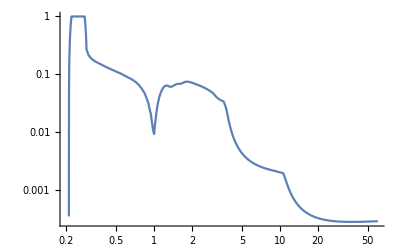

0.05 | 0.25 | 0.45 | 0.65 | 0.85 | 1.05 | 1.25 | 1.45 | 1.65 | 1.85 | 2.05 | 2.25 | 2.45 | 2.65 | 2.85 | 3.05 | 3.25 | 3.45 | 3.65 | 3.85 | 4.05 | 4.25 | 4.45 | 4.65 | 4.85
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.

```mathematica
(*Branching ratios*)
BrRatiosTable=Select[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/Scalar/decay widths/BrRatios.dat"}],"Table"],#[[1]]≠2&];
BrStoee[mS_]=Interpolation[BrRatiosTable[[All,{1,2}]],InterpolationOrder->1][mS];
BrStoμμ[mS_]=Interpolation[BrRatiosTable[[All,{1,3}]],InterpolationOrder->1][mS];
BrStoππ[mS_]=Interpolation[BrRatiosTable[[All,{1,4}]],InterpolationOrder->1][mS];
BrStoKK[mS_]=Interpolation[BrRatiosTable[[All,{1,5}]],InterpolationOrder->1][mS];
BrStoMultiπ[mS_]=Interpolation[BrRatiosTable[[All,{1,6}]],InterpolationOrder->1][mS];
BrStoGG[mS_]=Interpolation[BrRatiosTable[[All,{1,7}]],InterpolationOrder->1][mS];
BrStoττ[mS_]=Interpolation[BrRatiosTable[[All,{1,8}]],InterpolationOrder->1][mS];
BrStocc[mS_]=Interpolation[BrRatiosTable[[All,{1,9}]],InterpolationOrder->1][mS];
LogLogPlot[BrStoμμ[mS],{mS,0.2,60}]
(*Decays into "massless" particles: μμ, ee, ππ, 4π, 2G*)
BrRatioScalarMassless[mS_]=Interpolation[{#[[1]],#[[2]]+#[[3]]+#[[4]]+#[[6]]+#[[7]]}&/@BrRatiosTable,InterpolationOrder->1][mS];
BrRatioScalarK[mS_]=Interpolation[{#[[1]],#[[5]]}&/@BrRatiosTable,InterpolationOrder->1][mS];
BrRatioScalarτc[mS_]=Interpolation[{#[[1]],#[[8]]+#[[9]]}&/@BrRatiosTable,InterpolationOrder->1][mS];
Table[{mS,BrRatioScalarMassless[mS]+BrRatioScalarK[mS]+BrRatioScalarτc[mS]},{mS,0.05,5,0.2}]//Transpose//TableForm
```

## Compilable interpolation function mapping one grid into another

## 3D to 3D

```mathematica
nd=3;
cf3=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

## 4D to 4D

```mathematica
nd=4;
cf4=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

# Specifying the experiment

```mathematica
SetDirectory[NotebookDirectory[]];
(*Parent directory*)
NotebookDirectory[]//ParentDirectory;
AcceptanceDirectory=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
ExperimentDirectoriesList=Select[FileNames["*",AcceptanceDirectory,1],DirectoryQ];
(*List of available experiments (for which the geometry has been implemented)*)
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
ExperimentsListTemp2=Join[Partition[ExperimentsListTemp,1],Table[{TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"Acceptances",ExperimentsListTemp[[i]],ToString@StringForm["Acceptance_``_for_Scalar.m",ExperimentsListTemp[[i]]]}]},{i,1,Length[ExperimentsListTemp]}],2];
Print["List of available experiments:"]
ExperimentsList=Select[ExperimentsListTemp2,#[[2]]==True&][[All,1]]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiment:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
SelectedExperiment=If[Length[ExperimentsList]≠0,dropdownDialog[ExperimentsList,"Select the experiment:"]]
```

List of available experiments:

{advSNDnear,DarkQuest,DarkQuest-phase-2,FACET,FACET-FCC,LHCb-far-no-kinematics,MATHUSLA,SHADOWS-LoI,SHiP,SHiP-ECN3}

Selected experiment:

MATHUSLA

## Cross-sections, acceptances

```mathematica
dataAcceptances=Import[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"Acceptances",SelectedExperiment,ToString@StringForm["Acceptance_``_for_Scalar.m",SelectedExperiment]}]}],"MX"];//AbsoluteTiming
FacilityGivenExperiment=dataAcceptances[[1]];
ECALoption=dataAcceptances[[2]];
BrVis[mS_]=If[ECALoption=="False",BrVisCharged[mS],1];
FullAcceptanceData0=dataAcceptances[[3]];
{θminExpAll,θmaxExpAll}=MinMax[FullAcceptanceData0[[All,2]]];
{θminExp,θmaxExp}=MinMax[Select[FullAcceptanceData0,#[[6]]≠0&][[All,2]]];
{zminExp,zmaxExp}=MinMax[FullAcceptanceData0[[All,4]]];
AzimuthalAcceptanceData=DeleteDuplicatesBy[FullAcceptanceData0,{#[[2]],#[[4]]}&][[All,{2,4,5}]];//AbsoluteTiming
θGrid=DeleteDuplicates[AzimuthalAcceptanceData[[All,1]]];
zminmaxθdata=Table[MinMax[Select[AzimuthalAcceptanceData,#[[1]]==θGrid[[i]]&&#[[3]]≠0&][[All,2]]],{i,1,Length[θGrid],1}];
zminθ[θS_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{1}]],2],InterpolationOrder->1][θS];
zmaxθ[θS_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{2}]],2],InterpolationOrder->1][θS];
AzimuthalAcceptanceScalar[θS_,zS_]=Interpolation[AzimuthalAcceptanceData,InterpolationOrder->1][θS,zS];
DecAccDataLogarithmizedComp=Hold@Compile[{{FullAcceptanceData,_Real,2}},{Log10[#[[1]]],#[[2]],Log10[#[[3]]],#[[4]],If[#[[6]]≠0,Log10[#[[6]]],-90.]}&/@FullAcceptanceData]//ReleaseHold;
DecayAcceptanceScalar[mS_,θS_,ES_,zS_]=BrVis[mS]*10^(Interpolation[DecAccDataLogarithmizedComp[FullAcceptanceData0],InterpolationOrder->1][Log10[mS],θS,Log10[ES],zS]);//AbsoluteTiming
(*Interpolation for the full acceptance*)
acccomp=Hold@Compile[{{data,_Real,2}},{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]],If[#[[5]]*#[[6]]==0,-90,Log10[#[[5]]*#[[6]]]]}&/@SortBy[data,{#[[1]],#[[2]],#[[3]],#[[4]]}&]]//ReleaseHold;
(*Interpolation for the full acceptance*)
FullAcceptanceData=acccomp[FullAcceptanceData0];//AbsoluteTiming
FullAcceptanceScalar[mS_,θS_,ES_,zS_]=10^(Interpolation[FullAcceptanceData,InterpolationOrder->1][Log10[mS],Log10[θS],Log10[ES],Log10[zS]]);//AbsoluteTiming
dataCrossSections=dataAcceptances[[4]]//Transpose;
NpotGivenExperiment=Select[dataCrossSections,#[[1]]=="N_PoT"&][[1]][[2]]//N;
infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]
(*Total number of b b̄ and h*)
χProd["Bmixing"]=χProd["Bquartic"]=χProd["BsQuartic"]=Select[dataCrossSections,#[[1]]=="χ_(b or OverscriptBox[b, _])"&][[1]][[2]];
χProd["hQuartic"]=Select[dataCrossSections,#[[1]]=="χ_h"&][[1]][[2]];
{{"χ_(b or OverscriptBox[b, _])","χ_h"},{χProd["Bmixing"],χProd["hQuartic"]}}//TableForm
Row[{"Search for scalars at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

{0.921259,Null}

{3.7889,Null}

{4.37414,Null}

{2.43311,Null}

{2.80963,Null}

χ_(b or OverscriptBox[b, _]) | χ_h
0.0172222 | 7.63889×10^-10

Search for scalars at MATHUSLA located at LHC. N_collisions = 2.16×10^17

Quantity | θ_min, rad | θ_max, rad | θ_min(ϵ_dec), rad | θ_max(ϵ_dec), rad | z_min, m | z_max, m
Description | Min angle covered by experiment | Max angle covered by experiment | Min angle where ϵ_decay≠0 | Max angle where ϵ_decay≠0 | Min long. displacement of the decay volume | Max long. displacement of the decay volume
Value | 0.343377 | 0.957449 | 0.343377 | 0.957449 | 68. | 168.

# Number of events

## Angle-energy distributions and differential yields for the given experiment

## Checking whether all distributions are present

```mathematica
ScalarDistributionFileNames=Join[{ToString@StringForm["DoubleDistr-Scalars-From-B-mixing-``.dat",Sequence@@{FacilityGivenExperiment}],ToString@StringForm["DoubleDistr-Scalars-From-B-quartic-``.dat",Sequence@@{FacilityGivenExperiment}],ToString@StringForm["DoubleDistr-Scalars-From-Bs-quartic-``.dat",Sequence@@{FacilityGivenExperiment}]},If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",{ToString@StringForm["DoubleDistr-Scalars-From-h-quartic-``.dat",Sequence@@{FacilityGivenExperiment}]},{}]];
Do[If[!TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/",ScalarDistributionFileNames[[j]]}],Print[ScalarDistributionFileNames[[j]]," does not exist. Generate it using module 2!"]
],{j,1,Length[ScalarDistributionFileNames],1}]
Print["Production channels list:"]
(*Production from Higgses only*)
ProductionListNoBrem=Join[{"Bmixing","Bquartic","BsQuartic"},If[FacilityGivenExperiment=="LHC"||FacilityGivenExperiment=="FCC-hh",{"hQuartic"},{}]]
ProductionList=Join[ProductionListNoBrem,If[FacilityGivenExperiment=="FermilabBD"&&θminExp<θmaxBremFacility[FacilityGivenExperiment],{"Brem"},{}]]
```

Production channels list:

{Bmixing,Bquartic,BsQuartic,hQuartic}

{Bmixing,Bquartic,BsQuartic,hQuartic}

## Importing and interpolating

### Importing distributions

```mathematica
dataDistr[filename_]:=Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/Scalars/",filename}],"Table"]
Do[(*Data with the tabulated distribution*)
DataDistrScalar[ProductionList[[i]]]=dataDistr[ScalarDistributionFileNames[[i]]];
(*Its interpolation*)
DoubleDistrScalar[mS_,θS_,ES_,ProductionList[[i]]]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@DataDistrScalar[ProductionList[[i]]],InterpolationOrder->1][Log10[mS],Log10[θS],Log10[ES]]);
(*Min/mass mass of the FIP from the data*)
mlistScalar[ProductionList[[i]]]=DeleteDuplicates[DataDistrScalar[ProductionList[[i]]][[All,1]]];
{mminScalar[ProductionList[[i]]],mmaxScalar[ProductionList[[i]]]}=MinMax[mlistScalar[ProductionList[[i]]]];
(*Probability to produce the scalar per PoT*)
χXtimesχXtoScalar[mS_,θ2_,BrhToSS_,ProductionList[[i]]]=χProd[ProductionList[[i]]]*χMotherToS[mS,θ2,BrhToSS,ProductionList[[i]],FacilityGivenExperiment],{i,1,Length[ProductionListNoBrem],1}
]
(*For brem*)
If[FacilityGivenExperiment=="FermilabBD"&&θminExp<θmaxBremFacility[FacilityGivenExperiment],
DataDistrScalar["Brem"]=TableBremDistr[θminExp,θmaxExp,FacilityGivenExperiment];
DoubleDistrScalar[mS_,θS_,ES_,"Brem"]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-90]}&/@DataDistrScalar["Brem"],InterpolationOrder->1][Log10[mS],Log10[θS],Log10[ES]]);
mlistScalar["Brem"]=DeleteDuplicates[DataDistrScalar["Brem"][[All,1]]];
{mminScalar["Brem"],mmaxScalar["Brem"]}=MinMax[mlistScalar["Brem"]];
χXtimesχXtoScalar[mS_,θ2_,BrhToSS_,"Brem"]=PbremFacility[mS,θ2,FacilityGivenExperiment];
]
```

### Determining min/max energies of scalars for the given polar angle. Needed for better stability of Monte-Carlo integration

#### Common definition

```mathematica
EfromXmax[mass_,data_,LogMin_]:=Module[{distr},
datt=Select[data,#[[1]]==mass&];
EmaxVal=datt[[All,3]]//Max;
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/5}];
distr[θfip_,Efip_]=Abs[Evaluate[Interpolation[{#[[2]],#[[3]],#[[4]]+10^-90}&/@datt,InterpolationOrder->1][θfip,Efip]]];
DoubleDistrIntList[i_]:=Interpolation[ParallelTable[{Efip,Quiet[NIntegrate[distr[θfip,Efip],{θfip,θlist[[i]],θlist[[i+1]]},Method->"AdaptiveMonteCarlo"]]},{Efip,Table[10^x,{x,Log10[1.1*mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[1.1*mass])/50.}]}],InterpolationOrder->1][Efip];
θfipdistrlist[Efip_]=Table[{(θlist[[i]]+θlist[[i+1]])/2,DoubleDistrIntList[i]},{i,1,Length[θlist]-1,1}];
θEmaxList=Table[{θfipdistrlist[Efip][[i]][[1]],SortBy[Table[{Efip,θfipdistrlist[Efip][[i]][[2]]},{Efip,mass,EmaxVal,1}],-#[[2]]&][[1]][[1]]},{i,1,Length[θfipdistrlist[Efip]],1}];
θEmaxListInt[θfip_]=Interpolation[θEmaxList,InterpolationOrder->1][θfip];
NormVals=Table[NIntegrate[θfipdistrlist[Efip][[i]][[2]]+10^-90.,{Efip,mass,EmaxVal},Method->"InterpolationPointsSubdivision"],{i,1,Length[θfipdistrlist[Efip]],1}];
cdf[es_,i_]:=1-1/NormVals[[i]] NIntegrate[θfipdistrlist[Efip][[i]][[2]],{Efip,mass,es},Method->"InterpolationPointsSubdivision"];
cdftab[Efip_]=Table[{θfipdistrlist[Efip][[i]][[1]],Interpolation[ParallelTable[{10^es,Quiet[cdf[10^es,i]]},{es,Log10[mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[mass])/50}],InterpolationOrder->1][Efip]},{i,1,Length[θfipdistrlist[Efip]],1}];
logmin[θfip_]=LogMin;
Estart[θfip_]=Min[2*θEmaxListInt[θfip],0.9*EmaxVal];
Emaxv[i_]:=If[NormVals[[i]]<10^-15,mass,10^(Efip/.FindRoot[Log10[cdftab[10^Efip][[i]][[2]]]==logmin[θEmaxList[[i]][[1]]],{Efip,Log10[Estart[θEmaxList[[i]][[1]]]],Log10[θEmaxList[[i]][[2]]],Log10[EmaxVal]}])];
tabtemp=Table[{θEmaxList[[i]][[1]],Emaxv[i]},{i,1,Length[θEmaxList],1}];
tab=Join[{{θminExp,tabtemp[[1]][[2]]}},Drop[Drop[tabtemp,1],-1],{{θmaxExp,tabtemp[[-1]][[2]]}}];
10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@tab,InterpolationOrder->1][Log10[θfip]])
]
```

#### For particular production channels

InterpolatingFunction::dmval: Input value {5.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{16.5204,Null}

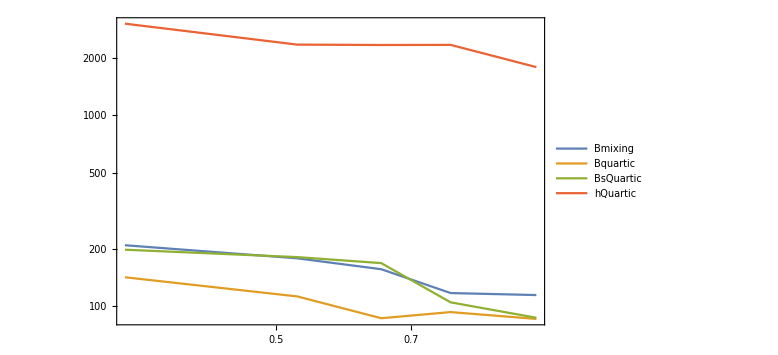

```mathematica
EmaxBlock[data_,logmin_]:=Module[{mlist},
mlist=Drop[data[[All,1]],-1];
EmaxTemp[m_,θ_]=Max[m,EfromXmax[mlist[[1]],data,logmin],EfromXmax[mlist[[-1]],data,logmin]]/.{θfip->θ};
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/10}];
10^(Interpolation[{#[[1]],Log10[#[[2]]],Log10[#[[3]]]}&/@Flatten[Table[{mfip,θfip,EmaxTemp[mfip,θfip]},{mfip,mlist[[1]],mlist[[-1]],(mlist[[-1]]-mlist[[1]])/10},{θfip,θlist}],{1,2}],InterpolationOrder->1][mfip,Log10[θfip]])
]
Do[EmaxScalar[mfip_,θfip_,prod]=EmaxBlock[DataDistrScalar[prod],-7],{prod,ProductionListNoBrem}]//AbsoluteTiming
If[FacilityGivenExperiment=="FermilabBD"&&θminExp<θmaxBremFacility[FacilityGivenExperiment],EmaxScalar[mfip_,θfip_,"Brem"]=ESmaxFromBrem[mfip,θfip,FacilityGivenExperiment];]
LogLogPlot[Evaluate[Table[EmaxScalar[0.1,θS,prod],{prod,ProductionList}]],{θS,θminExp,θmaxExp},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]]
```

## Number of events

## Estimate of the lower and upper bounds of the sensitivity

### Acceptances

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {45.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {55.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {62.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {45.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {55.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {62.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {45.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {55.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {62.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {61.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{62.3031,Null}

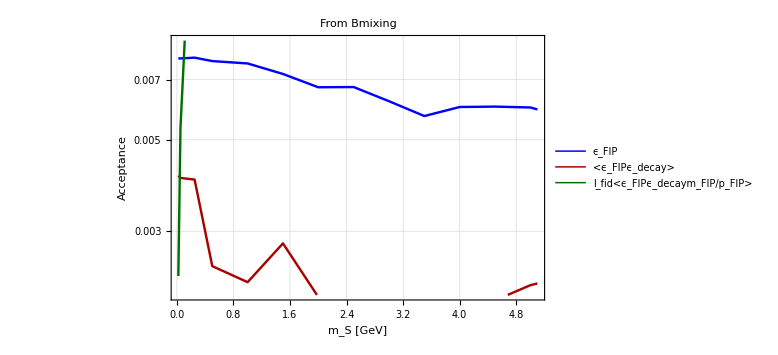
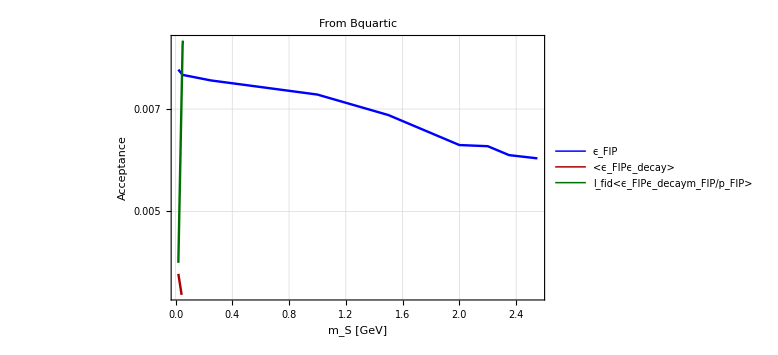
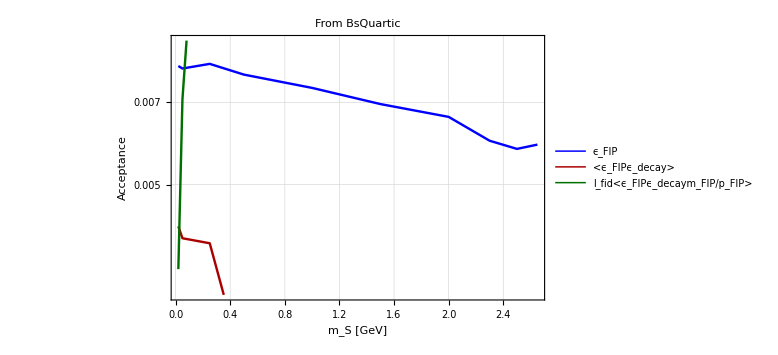
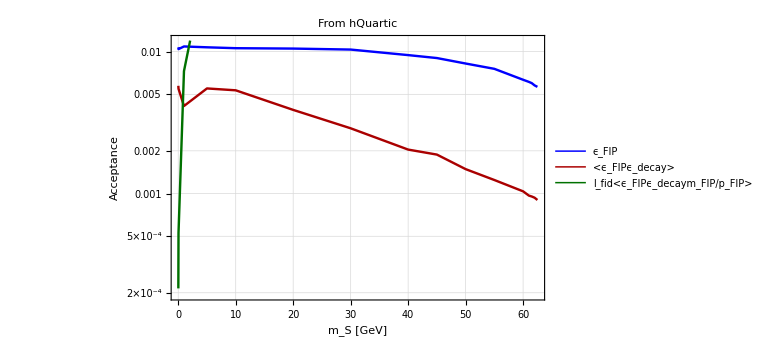

```mathematica
IntegrandWithϵAz[mS_,θS_,ES_,zS_,ProdChannel_]:=(DoubleDistrScalar[mS,θS,ES,ProdChannel]/Cos[θS])*AzimuthalAcceptanceScalar[θS,zS]
IntegrandWithϵAzϵDec[mS_,θS_,ES_,zS_,ProdChannel_]:=(DoubleDistrScalar[mS,θS,ES,ProdChannel]/Cos[θS])*AzimuthalAcceptanceScalar[θS,zS]*DecayAcceptanceScalar[mS,θS,ES,zS]
IntegrandWithϵAzϵDecγInv[mS_,θS_,ES_,zS_,ProdChannel_]:=(DoubleDistrScalar[mS,θS,ES,ProdChannel]/Cos[θS])*AzimuthalAcceptanceScalar[θS,zS]*DecayAcceptanceScalar[mS,θS,ES,zS](mS/(√(ES^2-mS^2)))
IntegrandGeomAcceptanceList[mS_,θS_,ES_,zS_,ProdChannel_]:={IntegrandWithϵAz[mS,θS,ES,zS,ProdChannel],IntegrandWithϵAzϵDec[mS,θS,ES,zS,ProdChannel],IntegrandWithϵAzϵDecγInv[mS,θS,ES,zS,ProdChannel]};
Do[IntegrandGeomAcceptance[mS_,θS_,ES_,zS_,prod]=IntegrandGeomAcceptanceList[mS,θS,ES,zS,prod],{prod,ProductionList}]
GeomAcceptanceScalar[mS_,i_,ProdChannel_]:=(1/(zmaxExp-zminExp))NIntegrate[IntegrandGeomAcceptance[mS,θS,ES,zS,ProdChannel][[i]],{θS,θminExp,θmaxExp},{ES,mS,EmaxScalar[mS,θS,ProdChannel]},{zS,zminθ[θS],zmaxθ[θS]},Method->"AdaptiveMonteCarlo"]
ϵGeomTabProdChannel[ProdChannel_]:=ParallelTable[{mS,GeomAcceptanceScalar[mS,1,ProdChannel],GeomAcceptanceScalar[mS,2,ProdChannel],(zmaxExp-zminExp)GeomAcceptanceScalar[mS,3,ProdChannel]},{mS,mlistScalar[ProdChannel]}]
Do[ϵGeomTabs[prod]=ϵGeomTabProdChannel[prod],{prod,ProductionList}]//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]]},FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{0.9Min[ϵGeomTabs[ProdChannel][[All,4]]],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m_S [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"ϵ_FIP","<ϵ_FIPϵ_decay>","l_fid<ϵ_FIPϵ_decaym_FIP/p_FIP>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1,1,1,1}]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data/Scalars",SelectedExperiment}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data/Scalars",SelectedExperiment}]]];
Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_Scalar_at_``_From_``.dat",Sequence@@{SelectedExperiment,prod}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/Scalars",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod],"Table"],{prod,ProductionList}]
```

```mathematica
ProductionList["Bmixing"]
```

{Bmixing,Bquartic,BsQuartic}(Bmixing)

### Lower and upper bounds

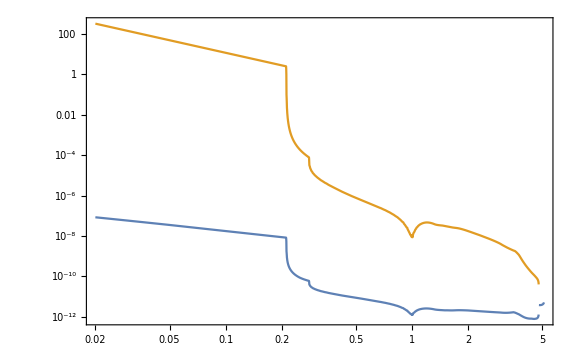

```mathematica
BrhToSSreference=0.15;
factorBounds["Bmixing"]=factorBounds["Brem"]=1;
factorBounds["Bquartic"]=factorBounds["BsQuartic"]=factorBounds["hQuartic"]=2;
Do[θ2minEstimate[mS_,prod]=((NpotGivenExperiment*χXtimesχXtoScalar[mS,1,BrhToSSreference,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][mS])/(2.3cτScalar[mS,1]))^(-1/2 factorBounds[prod]);
θ2maxEstimate[mS_,prod]=If[prod=="Bmixing",Re[Evaluate[-ProductLog[-1,-2.3*b/a]/b/.{a-> NpotGivenExperiment*χXtimesχXtoScalar[mS,1,BrhToSSreference,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][mS],b->zminExp/ldecayScalar[mS,1,EmaxScalar[mlistScalar[prod][[1]],θminExp,prod]]}]],ldecayScalar[mS,1,EmaxScalar[mlistScalar[prod][[1]],θminExp,prod]]/zminExp Log[(NpotGivenExperiment*χXtimesχXtoScalar[mS,1,BrhToSSreference,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][mS])/2.3]],{prod,ProductionList}]
ϵestplot="Bmixing";
LogLogPlot[{θ2minEstimate[mS,ϵestplot],θ2maxEstimate[mS,ϵestplot]},{mS,Min[mlistScalar[ϵestplot]],Max[mlistScalar[ϵestplot]]},Frame->True,ImageSize->Large]
```

## Number of events - brute-force integral

### Preliminary definitions

```mathematica
(*Differential decay probability 1/ldecay Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
PdecayDensity[mS_,θ2_,θS_,ES_,zS_]=Exp[-zS/(Cos[θS]*ldecayScalar[mS,θ2,ES])]/(Cos[θS]*ldecayScalar[mS,θ2,ES]);
(*The integrand determining the differential rate for events*)
Do[IntegrandScalar[mS_,θ2_,θS_,ES_,zS_,prod]=DoubleDistrScalar[mS,θS,ES,prod]*PdecayDensity[mS,θ2,θS,ES,zS]*AzimuthalAcceptanceScalar[θS,zS]*Min[DecayAcceptanceScalar[mS,θS,ES,zS],1],{prod,ProductionList}];
IntegralScalar[mS_,θ2_,ProdChannel_]:=NIntegrate[Abs[IntegrandScalar[mS,θ2,θS,ES,z,ProdChannel]],{θS,θminExp,θmaxExp},{ES,mS,EmaxScalar[mS,θS,ProdChannel]},{z,zminθ[θS],zmaxθ[θS]},Method->"AdaptiveMonteCarlo"]
θ2vall=10^-10;
(*ParallelTable[IntegralScalar[(mSmin[prod]+mSmax[prod])/2,θ2vall,prod],{prod,ProductionList}]*)
```

### Number of events

```mathematica
Nevents[mS_,θ2_,BrhToSS_,ProdChannel_]:=If[mminScalar[ProdChannel]≤mS≤mmaxScalar[ProdChannel]&&BrVis[mS]!=0,If[0.3*θ2minEstimate[mS,ProdChannel]<θ2<1.8θ2maxEstimate[mS,ProdChannel],NpotGivenExperiment*χXtimesχXtoScalar[mS,θ2,BrhToSS,ProdChannel]*IntegralScalar[mS,θ2,ProdChannel],0],0]
tabNev[mS_,BrhToSS_,ProdChannel_]:=ParallelTable[{10^θ2,Nevents[mS,10^θ2,BrhToSS,ProdChannel]},{θ2,-17,-4,0.1}]
(*ListLogLogPlot[{tabNev[0.6,0,"Bmixing"],Table[{10^x,1},{x,-15,-4,0.1}]},Joined->True,Frame->True,ImageSize->Large,PlotRange->{All,{10^-3,1000}}]*)
```

### At the lower bound (works only in the regime cτ<γ> >> l_experiment) - simplified expression

```mathematica
Do[NeventsLowerBoundMother[mS_,θ2_,BrhToSS_,prod]=If[mminScalar[prod]≤mS≤mmaxScalar[prod],Evaluate[(NpotGivenExperiment*χXtimesχXtoScalar[mS,θ2,BrhToSS,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][mS])/cτScalar[mS,θ2]]],{prod,ProductionList}];
NeventsLowerBoundTotal[mS_,θ2_,BrhToSS_]=Sum[NeventsLowerBoundMother[mS,θ2,BrhToSS,prod],{prod,ProductionList}];
(*LogLogPlot[Evaluate[Table[√(2.3/NeventsLowerBoundMother[mS,1,0.15,prod]),{prod,ProductionList}]],{mS,0.02,3},Frame->True,FrameStyle->Directive[Black, 22],ImageSize->Large,FrameLabel->{"m_S [GeV]","Lower bound of the 90%CL sensitivity"},PlotLabel-> Style["BC1", 20, Black],PlotLegends->Placed[{Style[#, 18]&/@ProductionList},Right],PlotStyle->{{Thickness[0.0045],Blue},{Thickness[0.0045],Darker@Red},{Thickness[0.0045],Darker@Darker@Green},{Thickness[0.0045],Darker@Cyan},{Thickness[0.0045],Magenta},{Thickness[0.0045],Black}},GridLines->Automatic]*)
```

## Number of events - alternative

### Preliminary definitions

#### In grid

```mathematica
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S], Subscript[z, S] for the initial acceptance data, logarithmized*)
{InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ}=DeleteDuplicates[FullAcceptanceData[[All,#]]]&/@{1,2,3,4};
(*Array of values of the initial acceptance data, reshaped*)
ϵvals=ArrayReshape[FullAcceptanceData[[All,5]],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
(*_________________________________________________________________*)
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S] for the initial FIP distribution data, logarithmized*)
DataLogarithmiedComp=Hold@Compile[{{data,_Real,2}},Table[If[data[[i]][[4]]==0,-90.,Log10[data[[i]][[4]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold
BlockGridsValsDistr[ProdChannel_]:=Module[{GridIn,vals},
GridIn=Log10[DeleteDuplicates[DataDistrScalar[ProdChannel][[All,#]]]&/@{1,2,3}];
vals=ArrayReshape[DataLogarithmiedComp[DataDistrScalar[ProdChannel]],{Length[GridIn[[1]]],Length[GridIn[[2]]],Length[GridIn[[3]]]}];
{GridIn,vals}
]
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod],{prod,ProductionList}];
```

CompiledFunction[…]

#### Out grid

```mathematica
(*Grid Subscript[θ, S], Subscript[z, S] for the final acceptance data, logarithmized*)
OutGridθfinal=(*InGridθϵ*)Log10[Table[x,{x,10^Min[InGridθϵ],10^Max[InGridθϵ],(10^Max[InGridθϵ]-10^Min[InGridθϵ])/30}]];
OutGridzfinal=Log10[Table[x,{x,10^InGridzϵ[[1]],10^InGridzϵ[[-1]],Min[(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/5,Max[0.5,(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/30]]}]](*InGridzϵ*);
ΔxVals[list_]:=Join[{(list[[2]]-list[[1]])/2},Table[list[[i]]-list[[i-1]],{i,2,Length[list],1}]];
Δθvals=ΔxVals[10^OutGridθfinal];
Δzvals=ΔxVals[10^OutGridzfinal];
(*Final energy grid. Mass- and production channel-dependent*)
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<300},{40,300≤Efip<700},{50,700≤Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
With[{start=1.01m,end=EmaxScalar[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N
]
ΔxValsTotComp=Hold@Compile[{{Δθvals,_Real,1},{ΔEvals,_Real,1},{Δzvals,_Real,1}},Table[{Δθvals[[i]]*ΔEvals[[j]]*Δzvals[[k]]},{i,1,Length[Δθvals]},{j,1,Length[ΔEvals]},{k,1,Length[Δzvals]}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold;
```

### Number of events

```mathematica
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
TableIntegrandDiscret[m_,ProdChannel_]:=Block[{},
OutGridEfinal=OutGridEnergy[N[m],ProdChannel];
ΔEvals=ΔxVals[10^OutGridEfinal];
ΔxValsTot=Flatten[ΔxValsTotComp[Δθvals,ΔEvals,Δzvals],{1,2,3}];
OutGridFinal=Tuples[{{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal}];
OutGridFinal1=10^OutGridFinal[[All,{2,3,4}]];
gϵ={InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ};
xgϵ={{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal};
xigϵ=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gϵ,xgϵ}];
ϵResult=10^Flatten@cf4[Sequence@@xigϵ,ϵvals];
gDistr={GridInFinal[ProdChannel][[1]],GridInFinal[ProdChannel][[2]],GridInFinal[ProdChannel][[3]]};
xgDistr={{Log10[N[m]]},OutGridθfinal,OutGridEfinal};
xigDistr=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gDistr,xgDistr}];
DistrResult=10^Flatten@cf3[Sequence@@xigDistr,DistrVals[ProdChannel]];
TabTemp0=Join[OutGridFinal1,List/@Flatten[DistrResult Partition[ϵResult,Length[OutGridzfinal]]],ΔxValsTot,2]
]
(*Values Subscript[f, FIP]×Subscript[ϵ, FIP]×Exp[-Subscript[z, FIP]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])×Subscript[ϵ, decay] Subscript[Δz, FIP] Subscript[ΔE, FIP] Subscript[Δθ, FIP] for the grid of values Subscript[θ, FIP], Subscript[E, FIP], Subscript[z, FIP] fixed values of Subscript[cτ, FIP] and Subscript[m, FIP]*)
(*tableprefac=Hold@Compile[{{tabb,_Real,2},{m,_Real},{cτ,_Real}},{(*#[[1]],#[[2]],#[[3]],*)Exp[-#[[3]]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-m^2))/m)]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-m^2))/m)#[[4]]*#[[5]]}&/@tabb,CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;*)
tableprefac=Hold@Compile[{{tabb,_Real,1},{m,_Real},{cτ,_Real}},Module[{angles,energies,zv,values,Δs,prefactor},
angles=Compile`GetElement[tabb,1];
energies=Compile`GetElement[tabb,2];
zv=Compile`GetElement[tabb,3];
values=Compile`GetElement[tabb,4];
Δs=Compile`GetElement[tabb,5];
prefactor=Exp[-zv/(Cos[angles]*cτ*(√(energies^2-m^2))/m)]/(Cos[angles]*cτ*(√(energies^2-m^2))/m);
prefactor*Δs*values],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation of the values above*)
sumcompile=Hold@Compile[{{tabcτm,_Real,1}},Total[tabcτm],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold;
{mminϵ,mmaxϵ}=10^MinMax[InGridmϵ];
(*Number of events*)
NeventsDiscret[m_,ProdChannel_,BrhToSS_,θ2list_]:=Module[{NevDiscret,NpotTimesχval},
If[Max[mminϵ,mminScalar[ProdChannel]]<m<Min[mmaxScalar[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel];
NpotTimesχval[θ2_]=NpotGivenExperiment*χXtimesχXtoScalar[m,θ2,BrhToSS,ProdChannel];
{lowerbound,upperbound}={θ2minEstimate[m,ProdChannel],θ2maxEstimate[m,ProdChannel]};
brvis=BrVis[m];
NevDiscret[θ2_]:=If[brvis!=0,If[0.3lowerbound<θ2<1.5upperbound,NpotTimesχval[θ2]*brvis*sumcompile[tableprefac[integrandtab,m,cτScalar[m,θ2]]],0],0];
Table[{m,θ2list[[i]],NevDiscret[θ2list[[i]]]},{i,1,Length[θ2list],1}],Table[{m,θ2list[[i]],0},{i,1,Length[θ2list],1}]]
]
```

#### Test

```mathematica
mtest=0.5;
ProdTest="Bmixing";
θ2list=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-17.,-3.,0.3}];
dat1=NeventsDiscret[mtest,ProdTest,BrhToSSreference,θ2list];//AbsoluteTiming
dat2=ParallelTable[{θ2list[[i]],cτScalar[mtest,θ2list[[i]]],Nevents[mtest,θ2list[[i]],BrhToSSreference,ProdTest]},{i,1,Length[θ2list],1}];//AbsoluteTiming
Join[dat1,dat2[[All,{3,2}]],2]//TableForm
```

{0.161001,Null}

{17.7647,Null}

0.5 | 1.×10^-17 | 0 | 0 | 7.96518×10^8
0.5 | 1.99526×10^-17 | 0 | 0 | 3.99205×10^8
0.5 | 3.98107×10^-17 | 0 | 0 | 2.00076×10^8
0.5 | 7.94328×10^-17 | 0 | 0 | 1.00276×10^8
0.5 | 1.58489×10^-16 | 0 | 0 | 5.02569×10^7
0.5 | 3.16228×10^-16 | 0 | 0 | 2.51881×10^7
0.5 | 6.30957×10^-16 | 0 | 0 | 1.2624×10^7
0.5 | 1.25893×10^-15 | 0 | 0 | 6.32697×10^6
0.5 | 2.51189×10^-15 | 0 | 0 | 3.17099×10^6
0.5 | 5.01187×10^-15 | 0 | 0 | 1.58926×10^6
0.5 | 1.×10^-14 | 0 | 0 | 796518.
0.5 | 1.99526×10^-14 | 0 | 0 | 399205.
0.5 | 3.98107×10^-14 | 0 | 0 | 200076.
0.5 | 7.94328×10^-14 | 0 | 0 | 100276.
0.5 | 1.58489×10^-13 | 0 | 0 | 50256.9
0.5 | 3.16228×10^-13 | 0 | 0 | 25188.1
0.5 | 6.30957×10^-13 | 0 | 0 | 12624.
0.5 | 1.25893×10^-12 | 0 | 0 | 6326.97
0.5 | 2.51189×10^-12 | 0 | 0 | 3170.99
0.5 | 5.01187×10^-12 | 0.724296 | 0.729898 | 1589.26
0.5 | 1.×10^-11 | 2.84149 | 2.85776 | 796.518
0.5 | 1.99526×10^-11 | 10.9899 | 11.2548 | 399.205
0.5 | 3.98107×10^-11 | 41.3559 | 41.5715 | 200.076
0.5 | 7.94328×10^-11 | 147.867 | 153.177 | 100.276
0.5 | 1.58489×10^-10 | 482.769 | 483.41 | 50.2569
0.5 | 3.16228×10^-10 | 1355.05 | 1363.84 | 25.1881
0.5 | 6.30957×10^-10 | 3007.75 | 2902.55 | 12.624
0.5 | 1.25893×10^-9 | 4739.68 | 4839.34 | 6.32697
0.5 | 2.51189×10^-9 | 4664.83 | 4695.99 | 3.17099
0.5 | 5.01187×10^-9 | 2557.71 | 2593.4 | 1.58926
0.5 | 1.×10^-8 | 762.279 | 772.259 | 0.796518
0.5 | 1.99526×10^-8 | 138.36 | 143.157 | 0.399205
0.5 | 3.98107×10^-8 | 15.4868 | 15.882 | 0.200076
0.5 | 7.94328×10^-8 | 0.535095 | 0.53139 | 0.100276
0.5 | 1.58489×10^-7 | 0.00134501 | 0.00129399 | 0.0502569
0.5 | 3.16228×10^-7 | 3.84438×10^-8 | 3.38606×10^-8 | 0.0251881
0.5 | 6.30957×10^-7 | 8.97881×10^-16 | 8.54048×10^-16 | 0.012624
0.5 | 1.25893×10^-6 | 0 | 5.52795×10^-29 | 0.00632697
0.5 | 2.51189×10^-6 | 0 | 0 | 0.00317099
0.5 | 5.01187×10^-6 | 0 | 0 | 0.00158926
0.5 | 0.00001 | 0 | 0 | 0.000796518
0.5 | 0.0000199526 | 0 | 0 | 0.000399205
0.5 | 0.0000398107 | 0 | 0 | 0.000200076
0.5 | 0.0000794328 | 0 | 0 | 0.000100276
0.5 | 0.000158489 | 0 | 0 | 0.0000502569
0.5 | 0.000316228 | 0 | 0 | 0.0000251881
0.5 | 0.000630957 | 0 | 0 | 0.000012624

### Differential number of events

CompiledFunction[…]

{0.505,3003.1}

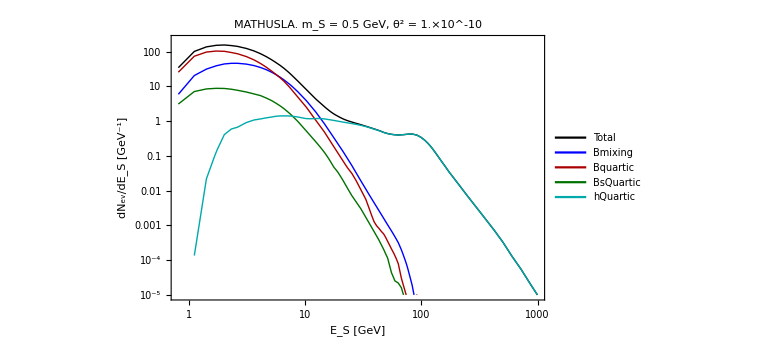

```mathematica
(*The same as tableprefac but also including the grid*)
tableGridPrefac=Hold@Compile[{{tabb,_Real,2},{mS,_Real},{cτ,_Real}},{#[[1]],#[[2]],#[[3]],Exp[-#[[3]]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)]/(Cos[#[[1]]]*cτ*(√((#[[2]])^2-mS^2))/mS)#[[4]]*#[[5]]}&/@tabb,CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation returning the differential number of events X, df/dX *)
NdiffCompiled=Hold@Compile[{{tabNdiff,_Real,2},{GridQuantity,_Real,1},{LengthPerVariable,_Integer},{NPoTtimesPprod,_Real}},Table[{tabNdiff[[LengthPerVariable*(i-1)+1]][[1]],NPoTtimesPprod*Sum[tabNdiff[[LengthPerVariable*(i-1)+j]][[4]],{j,1,LengthPerVariable,1}]},{i,1,Length[GridQuantity],1}],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold
(*Variable = "E_X","x_x","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_X" ->2,"θ_X"->1,"x_x"->3}]
(*Differential number of events*)
NeventsDifferentialDiscret[m_,ProdChannel_,θ2_,BrhToSS_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*χXtimesχXtoScalar[m,θ2,BrhToSS,ProdChannel];
tablegrid0=TableIntegrandDiscret[m,ProdChannel];
Δxvals:=Association[{"E_X"->ΔEvals,"θ_X"-> Δθvals,"x_X"-> Δzvals}];
Δxval=Δxvals[Variable];
cτVal=cτScalar[m,θ2];
brvis=BrVis[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
mvaltest=0.5;
θ2test=10^-10.;
BrhToSStest=0.01;
quantity="E_X";
LegendX:=Association[{"E_X"->"E_S [GeV]","θ_X"->"θ_S [rad]","x_X"-> "z_S [m]"}]
LegendY:=Association[{"E_X"->"dN_ev/dE_S [GeV^-1]","θ_X"->"dN_ev/dθ_S [rad^-1]","x_X"-> "dN_ev/dz_S [m^-1]"}]
prodlisttemp={};
Do[If[Max[mminϵ,mminScalar[prod]]<mvaltest<Min[mmaxScalar[prod],mmaxϵ],
prodlisttemp=Join[prodlisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscret[mvaltest,prod,θ2test,BrhToSStest,quantity];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,prodlisttemp}];
LegendList=Join[{"Total"},prodlisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,prodlisttemp}],1]//MinMax
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@prodlisttemp];
LogLogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@LegendList,{0.85,0.7}],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 23],PlotLabel->Style[Row[{SelectedExperiment,". m_S = ",mvaltest," GeV, θ^2 = ",(θ2test//N)}],20,Black]]
(*tt=NeventsDifferentialDiscret[0.5,"Bmixing",10^-11,0.15,"E_X"];
ListLogLogPlot[tt,PlotRange->{All,{10^-9,100}},Joined->True]
Sum[tt[[i]][[2]]*Δxval[[i]],{i,1,Length[tt],1}]*)
```

# Exporting tabulated number of events

## Definitions

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/Scalars"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/Scalars"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/Scalars",SelectedExperiment}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/Scalars",SelectedExperiment}]]];
Print["Filenames with tabulated N_events:"]
ListExport1:=Association[{"Bmixing"->"mixing","Bquartic"->"quartic","BsQuartic"->"quartic","hQuartic"->"quartic","Brem"->"mixing"}]
ListExport2:=Association[{"Bmixing"->"B","Bquartic"->"B","BsQuartic"->"Bs","hQuartic"->"h","Brem"->"Brem"}]
Do[FilenameNevents[prod]=ToString@StringForm["Nevents_Scalar_``_at_``_Npot=``_From_``.dat",Sequence@@{ListExport1[prod],SelectedExperiment,NpotGivenExperiment//CForm//ToString,ListExport2[prod]}],{prod,ProductionList}]
Table[FilenameNevents[prod],{prod,ProductionList}]//TableForm
mlistScalarExport["Brem"]={0.021,0.051,0.1,0.13,0.15,0.2,0.21,0.215,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.289,0.3,0.35,0.4,0.45,0.5,0.6,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.3,1.5,1.8,1.9,1.99,2.1,2.2,2.3,2.4,2.5};
mlistScalarExport["Bquartic"]={0.021,0.051,0.1,0.13,0.15,0.2,0.21,0.215,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.289,0.3,0.35,0.4,0.45,0.5,0.6,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.3,1.5,1.8,1.9,1.99,2.05,2.1,2.2,2.3,2.4,2.5,2.55};
mlistScalarExport["Bmixing"]={0.021,0.051,0.1,0.13,0.15,0.17,0.2,0.21,0.215,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.289,0.3,0.35,0.4,0.45,0.5,0.6,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.3,1.5,1.8,1.9,1.99,2.1,2.3,2.4,2.5,2.6,2.7,2.9,3,3.2,3.5,3.7,3.8,3.9,4,4.3,4.6,4.8,5,5.1};
mlistScalarExport["BsQuartic"]={0.021,0.051,0.1,0.13,0.15,0.17,0.2,0.21,0.215,0.22,0.23,0.25,0.26,0.28,0.289,0.3,0.35,0.5,0.6,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.3,1.5,1.8,1.9,1.99,2.05,2.1,2.2,2.3,2.4,2.5,2.55,2.6,2.65};
mlistScalarExport["hQuartic"]={0.021,0.051,0.1,0.13,0.15,0.17,0.2,0.21,0.215,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.289,0.3,0.35,0.4,0.45,0.5,0.6,0.7,0.8,0.85,0.9,0.95,0.99,1.02,1.05,1.1,1.3,1.5,1.8,1.9,1.99,2.1,2.3,2.5,2.6,2.7,2.9,3,3.2,3.5,3.7,3.8,3.9,4,4.3,4.6,4.8,5,5.1,7.,10.,10.6,12.,15.,20.,30.,40.,45.,50.,55.,60.,61.,62.,62.49};
θ2list=Table[10^x,{x,-20,-3,0.02}]//N;
```

Filenames with tabulated N_events:

Nevents_Scalar_mixing_at_MATHUSLA_Npot=2.16e17_From_B.dat
Nevents_Scalar_quartic_at_MATHUSLA_Npot=2.16e17_From_B.dat
Nevents_Scalar_quartic_at_MATHUSLA_Npot=2.16e17_From_Bs.dat
Nevents_Scalar_quartic_at_MATHUSLA_Npot=2.16e17_From_h.dat

## Exporting

## Common definition

```mathematica
BlockExport[ProdChannel_]:=Block[{},
If[Select[ProductionList,#==ProdChannel&]=={},,
mlist=mlistScalarExport[ProdChannel];
TabFrom=Monitor[Table[NeventsDiscret[mlist[[k]],ProdChannel,BrhToSSreference,θ2list],{k,1,Length[mlist],1}],Row[{ProgressIndicator[k,{1,Length[mlist]}],"i = ",k,"/",Length[mlist],", m = ",mlist[[k]]," GeV"}," "]];
Export[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/Scalars",SelectedExperiment,FilenameNevents[ProdChannel]}],Flatten[TabFrom,1],"Table"]]
]
```

## From B - mixing

```mathematica
BlockExport["Bmixing"];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {0.021} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.051} lies outside the range of data in the interpolating function. Extrapolation will be used.

{105.654,Null}

## From B - quartic

```mathematica
BlockExport["Bquartic"];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {0.021} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.051} lies outside the range of data in the interpolating function. Extrapolation will be used.

{93.5573,Null}

## From B_s - quartic

```mathematica
BlockExport["BsQuartic"];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {0.021} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.051} lies outside the range of data in the interpolating function. Extrapolation will be used.

{95.8372,Null}

## From h - quartic

```mathematica
BlockExport["hQuartic"];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {0.021} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.051} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{287.921,Null}

## From bremsstrahlung

```mathematica
BlockExport["Brem"];//AbsoluteTiming
```

{0.0000324,Null}

# Computing sensitivities

## Importing data and interpolations

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","Scalars"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","Scalars"}]]]
NeventsDirectory=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents","Scalars"}];
ExperimentDirectoriesListNevents=Select[FileNames["*",NeventsDirectory,1],DirectoryQ];
Print["List of available experiments with tabulated N_events for Scalars:"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiment:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
If[Length[ExperimentsListNevents]≠0,GivenExperimentForSensitivityComputation=dropdownDialog[ExperimentsListNevents,"Select the experiment:"]]
CondANUBIS=MemberQ[{"ANUBIS-1","ANUBIS-2","ANUBIS-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,Print["One of the modules of ANUBIS is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-1","ANUBIS-2","ANUBIS-3"}];
filesNevents={};
Do[filesNevents=Join[filesNevents,FileNames["*.dat",FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/Scalars",exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
(*Filenames=Table[{StringReplace[Last@FileNameSplit@files[[i]],{"e+0":>"*^","e-0":>"*^-"}]},{i,1,Length[files],1}];*)
Print["List of production channels:"]
FilenamesNevents=Table[Last@FileNameSplit@filesNevents[[i]],{i,1,Length[filesNevents],1}];
FilenameParameters[i_]:=StringCases[FilenamesNevents[[i]],"Nevents_Scalar_"~~coupling__~~"_at_"~~experiment__~~"_Npot="~~Npot__~~"_From_"~~mother__~~".dat":>{coupling,experiment,Npot,mother}][[1]]
ProductionChannelsList=Table[FilenameParameters[i],{i,1,Length[FilenamesNevents],1}][[All,{2,1,3,4}]]//DeleteDuplicates;
Join[{{"coupling type","Experiment","N_PoT","Mother particle"}},ProductionChannelsList]//TableForm
NpotDefault=Internal`StringToMReal[ProductionChannelsList[[1]][[3]]];
NeventsTabulatedList=Table[Import[filesNevents[[i]],"Table"],{i,1,Length[filesNevents],1}];
mSminmaxTabulated[i_]:=MinMax[Select[NeventsTabulatedList[[i]],#[[3]]>10^-30&][[All,1]]]
θ2minmaxTabulated[i_]:=MinMax[Select[NeventsTabulatedList[[i]],#[[3]]>10^-30&][[All,2]]]
mSminmaxOverall=MinMax[Table[mSminmaxTabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
θ2minmaxOverall=MinMax[Table[θ2minmaxTabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
NevintMixing[i_]:=If[mSminmaxTabulated[i][[1]]≤ mS≤mSminmaxTabulated[i][[2]]&&θ2minmaxTabulated[i][[1]]≤θ2≤ θ2minmaxTabulated[i][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulatedList[[i]],InterpolationOrder->1][Log10[mS],Log10[θ2]])],0]
BrhToSSreference=0.15;
NevintQuartic[i_]:=If[mSminmaxTabulated[i][[1]]≤ mS≤mSminmaxTabulated[i][[2]]&&θ2minmaxTabulated[i][[1]]≤θ2≤ θ2minmaxTabulated[i][[2]],Evaluate[BrhToSS/BrhToSSreference 10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulatedList[[i]],InterpolationOrder->1][Log10[mS],Log10[θ2]])],0]
NevIntList[mS_,θ2_,BrhToSS_]=Table[If[ProductionChannelsList[[i]][[2]]=="mixing",NevintMixing[i],NevintQuartic[i]],{i,1,Length[NeventsTabulatedList],1}];
NevTot[mS_,θ2_,BrhToSS_]=Sum[NevIntList[mS,θ2,BrhToSS][[i]],{i,1,Length[NevIntList[mS,θ2,BrhToSS]],1}];
ExperimentFolder=If[CondANUBIS==True,"ANUBIS",GivenExperimentForSensitivityComputation];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","Scalars",ExperimentFolder}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","Scalars",ExperimentFolder}]]]
```

List of available experiments with tabulated N_events for Scalars:

MATHUSLA
SHADOWS-LoI
SHiP-ECN3

Selected experiment:

MATHUSLA

List of production channels:

coupling type | Experiment | N_PoT | Mother particle
MATHUSLA | mixing | 2.16e17 | B
MATHUSLA | quartic | 2.16e17 | B
MATHUSLA | quartic | 2.16e17 | Bs
MATHUSLA | quartic | 2.16e17 | h

## Density plot for number of events

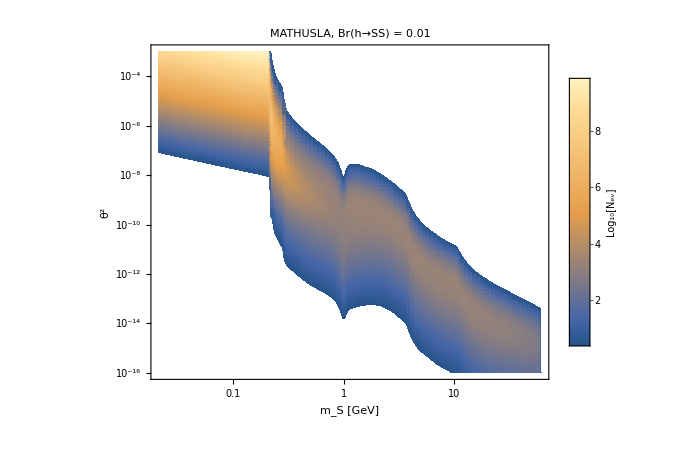

```mathematica
Nevmax=Max[Table[Max[NeventsTabulatedList[[i]][[All,3]]],{i,1,Length[NeventsTabulatedList],1}]];
BrhToSSval=0.01;
(*If the plot is not as smooth as it is desired, increase the value of PlotPoints option*)
plot=DensityPlot[Evaluate[Log10[NevTot[mS,θ2,BrhToSSval]]],{mS,mSminmaxOverall[[1]],mSminmaxOverall[[2]]},{θ2,θ2minmaxOverall[[1]],θ2minmaxOverall[[2]]},ScalingFunctions->{"Log","Log"},AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[Nevmax]}},ImageSize->Large,FrameLabel->{"m_S [GeV]","θ^2"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotPoints->100,PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[Nevmax]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder,", Br(h→SS) = ",BrhToSSval}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
(*Exporting. "AllowRasterization"->False option reduces the size of the output. Without this option, the file may be very large, depending on the value of PlotPoints*)
(*Export[FileNameJoin[{NotebookDirectory[],"NeventsDensityPlotExample.pdf"}],plot,"AllowRasterization"->False]*)
```

## Sensitivity computation

The value of Br(h->SS) for which the sensitivity will be computed:

0.01

The minimal value of N_events for which the sensitivity will be computed:

2.3

No

2.16×10^17

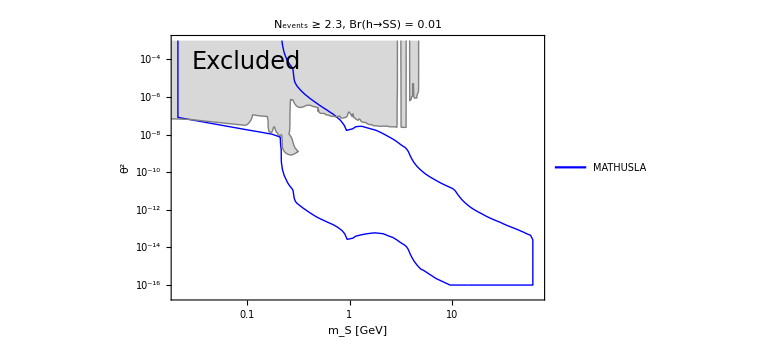

```mathematica
SensitivityBlock[Nev_,BrhToSSval_,Npot_]:=Block[{},
RegSens=RegionPlot[Npot/NpotDefault NevTot[10^mS,10^θ2,BrhToSSval]≥Nev,{mS,Log10[mSminmaxOverall[[1]]],Log10[mSminmaxOverall[[2]]]},{θ2,Log10[θ2minmaxOverall[[1]]],Log10[θ2minmaxOverall[[2]]]}];
(*Sens={10^#[[1]],10^#[[2]]}&/@Partition[Flatten[Cases[Normal@RegSens,Line[x_]:>x,Infinity]],2];*)
SensTemp=Cases[Normal@RegSens,Line[x_]:>x,Infinity];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp[[i]],{i,1,Length[SensTemp],1}];
Export[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","Scalars",GivenExperimentForSensitivityComputation,ToString@StringForm["Sensitivity_Scalar_at_``_BrhToSS=``_Nev=``_Npot=``.xls",Sequence@@{GivenExperimentForSensitivityComputation,BrhToSSval//ToString,Nev//ToString,Npot//CForm//ToString}]}],Sens];
Sens
]
Print["The value of Br(h->SS) for which the sensitivity will be computed:"]
BrhToSSval=DialogInput[{br=""},Column[{"Enter the value of Br(h->SS) for which the sensitivity will be computed (0 corresponds to BC4):",InputField[Dynamic[br],Number],Button["Proceed",DialogReturn[br],ImageSize->Automatic]}]]//N
Print["The minimal value of N_events for which the sensitivity will be computed:"]
NevMinVal=DialogInput[{nev=""},Column[{"Enter the value of N_events for which the sensitivity will be computed:",InputField[Dynamic[nev],Number],Button["Proceed",DialogReturn[nev],ImageSize->Automatic]}]]//N
choiceNPoT=dropdownDialog[{"Yes","No"},Row[{"The number of proton collisions is ", NpotDefault,". Would you like to change it?"}]]
If[choiceNPoT=="Yes",NpotSelected=DialogInput[{br=""},Column[{"Enter the number of proton collisions",InputField[Dynamic[br],String],Button["Proceed",DialogReturn[br],ImageSize->Automatic]}]]//ToExpression//N,NpotSelected=NpotDefault]
BC4excluded=Import[FileNameJoin[{NotebookDirectory[],"contours/Scalar/scalar-all-experiments.txt"}],"Table"];
sens=SensitivityBlock[NevMinVal,BrhToSSval,NpotSelected];
Show[ListLogLogPlot[Cases[{sens,BC4excluded},_?MatrixQ,All],Joined->{True,True,True,True}, Frame-> True,FrameLabel->{"m_S [GeV]" , "θ^2"},FrameStyle->Directive[Black, 23],PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]],ConstantArray[{Thick,Gray},1]},1],Filling->{Length[sens]+1->{Top,Directive[Gray,Opacity[0.3]]}},ImageSize->Large,PlotRange->{{1.01mSminmaxOverall[[1]],1.1mSminmaxOverall[[2]]},{0.3*Min[sens[[1]][[All,2]]],0.99θ2minmaxOverall[[2]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal,", Br(h→SS) = ",BrhToSSval}],18,Black],PlotLegends->Placed[Style[#,15]&/@{ExperimentFolder},{0.2,0.15}]](*,LogLogPlot[{x,x^2,x^3,x^4,x^5,x^6},{x,0.05,62.49},PlotStyle->{{Thickness[0.006],Blue},{Thickness[0.006],Darker@Red},{Thickness[0.006],Darker@Red,Dashing[0.02]},{Thickness[0.006],Black},{Thickness[0.01],Darker@Cyan,Dashing[0.007]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Red}},PlotLegends->Placed[Style[#,15]&/@{"SHiP","SHADOWS_(specified in LoI)","SHADOWS_(specified by Gaia)", "SHADOWS_(collab estimate)"},{0.26,0.15}]]*),Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.2,0.9}]]}]]
```